```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metadesc={Number,Number,Number,Number,Number,Number,Number,Word,Real,Real,Real,Real};
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l+int/2,u-int/2,int}]],3];
logo=Import["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis\\pbc-logo-v6.png"];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

All Good!

All Good 1 !

All Good 2 !

All Good 3 !

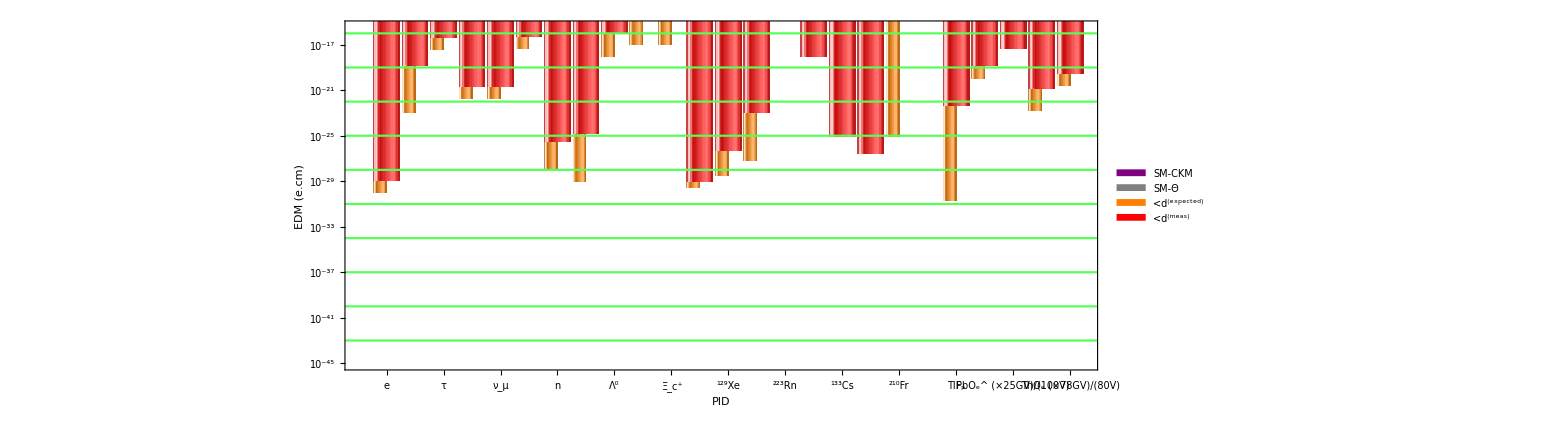

All Good!

All Good 1 !

All Good 2 !

All Good 3 !

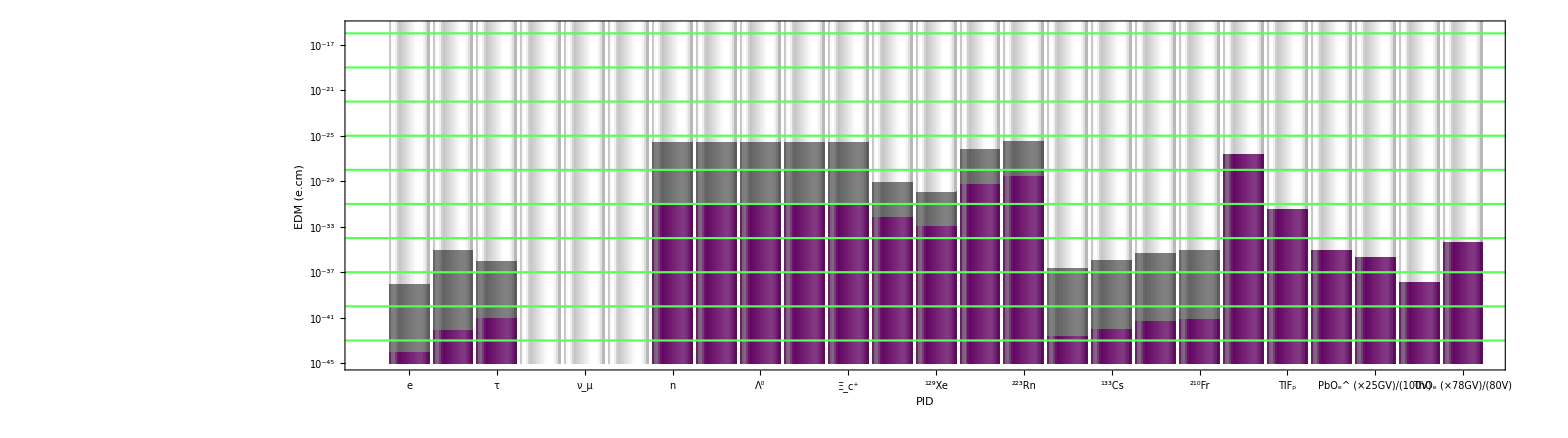

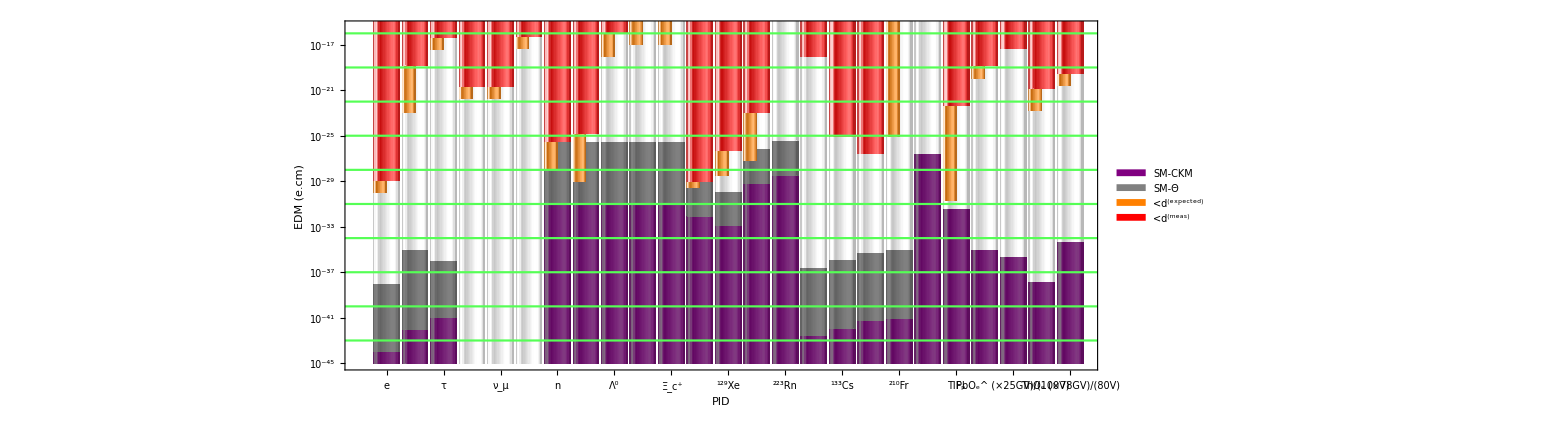

```mathematica
pttab1={
(*e*){{1,0},{1,0},{1,N[10^(-30)]},{0.5,1.1*N[10^(-29)]},{1,N[10^(-14)]}},
(*mu*){{1,0(*4.2*N[10^(-36)*)},{1,0},{1,N[10^(-23)]},{0.5,1.6*N[10^(-19)]},{1,N[10^(-14)]}},
(*τ*){{1,0},{1,0},{1,3.8*N[10^(-18)]},{0.5,3.8*N[10^(-17)]},{1,N[10^(-14)]}},(*Orange: 1order improvement, 3rd column changed*)
(*Subscript[ν, e]*){{1,0},{1,0},{1,2*N[10^(-22)]},{0.5,2*N[10^(-21)]},{1,N[10^(-14)]}},(*Orange: 1order improvement, 3rd column changed*)
(*Subscript[ν, μ]*){{1,0},{1,0},{1,2*N[10^(-22)]},{0.5,2*N[10^(-21)]},{1,N[10^(-14)]}},(*Orange: 1order improvement, 3rd column changed*)
(*Subscript[ν, τ]*){{1,0},{1,0},{1,4.35*N[10^(-18)]},{0.5,4.35*N[10^(-17)]},{1,N[10^(-14)]}},(*Orange: 1order improvement, 3rd column changed*)
(*n*){{1,0},{1,0},{1,N[10^(-28)]},{0.5,2.9*N[10^(-26)]},{1,N[10^(-14)]}},
(*p*){{1,0},{1,0},{1,N[10^(-29)]},{0.5,1.7*N[10^(-25)]},{1,N[10^(-14)]}},
(*Old-Use*)
(*(*Λ^0*){1*N[10^(-32)],4.4*N[10^(-26)],1.2*N[10^(-16)],N[10^(-14)]},
(*Σ^0*){3.3*N[10^(-33)],4.4*N[10^(-26)],N[10^(-10)],0},
(*Ξ^0*){1.3*N[10^(-32)],4.4*N[10^(-26)],N[10^(-10)],0},*)
(*NEW-don't use*)
(*Λ^0*){{1,0},{1,0},{1,N[10^(-18)]},{0.5,1.2*N[10^(-16)]},{1,N[10^(-14)]}},
(*Subscript[Λ, c]^+*){{1,0},{1,0},{1,N[10^(-17)]},{0.5,N[10^(-14)]},{1,0}},
(*Subscript[Ξ, c]^+*){{1,0},{1,0},{1,N[10^(-17)]},{0.5,N[10^(-14)]},{1,0}}
};
pttab2={
(*^199 Hg*){{1,0},{1,0},{1,3*N[10^(-30)]},{0.5,6.2*N[10^(-30)]},{1,N[10^(-14)]}},
(*^129 Xe*){{1,0},{1,0},{1,3*N[10^(-29)]},{0.5,5.4*N[10^(-27)]},{1,N[10^(-14)]}},
(*^225 Ra*){{1,0},{1,0},{1,6*N[10^(-28)]},{0.5,1.2*N[10^(-23)]},{1,N[10^(-14)]}},
(*^223 Rn*){{1,0},{1,0},{1,N[10^(-14)]},{1,0},{1,0}},
(*(*^239 Pu*){3.4*N[10^(-31)],4*N[10^(-29)],0,N[10^(-10)],0},*)
(*^89 Rb*){{1,0(*2*N[10^(-38)]*)},{1,0(*8.6*N[10^(-38)]*)},{1,1*N[10^(-18)]},{1,0},{1,N[10^(-14)]}},
(*^133 Cs*){{1,0(*2*N[10^(-38)]*)},{1,0(*8.6*N[10^(-38)]*)},{1,9.3*N[10^(-26)]},{1,0},{1,N[10^(-14)]}},
(*^205 Tl*){{1,0(*2*N[10^(-38)]*)},{1,0(*8.6*N[10^(-38)]*)},{1,2.6*N[10^(-27)]},{1,0},{1,N[10^(-14)]}},
(*^210 Fr*){{1,0(*2*N[10^(-38)]*)},{1,0(*8.6*N[10^(-38)]*)},{1,903*N[10^(-28)]},{0.5,1*N[10^(-14)]},{1,0}}
};
pttab3={
(*^225 RaF^+*){{1,0},{1,0},{1,N[10^(-14)]},{1,0}},
(*TlF*){{1,0},{1,0},{1,2*N[10^(-31)]},{0.5,4.8*N[10^(-23)]},{1,N[10^(-14)]}},
(*HfF^+*){{1,0*((N[10^(-44)])/(2*N[10^(-38)]))},{1,0},{1,1*N[10^(-20)]},{0.5,1.25*N[10^(-19)]},{1,N[10^(-14)]}},
(*PbO*){{1,0*((N[10^(-44)])/(2*N[10^(-38)]))},{1,0},{1,4.3*N[10^(-18)]},{1,0},{1,N[10^(-14)]}},
(*YbF*){{1,0*((N[10^(-44)])/(2*N[10^(-38)]))},{1,0},{1,1.54*N[10^(-21)]/90},{0.5,1.54*N[10^(-21)]},{1,N[10^(-14)]}},
(*ThO*){{1,0*((N[10^(-44)])/(2*N[10^(-38)]))*80/36},{1,0},{1,2*N[10^(-19)]*1.1/8.7*1.1/10},{0.5,2*N[10^(-19)]*1.1/8.7},{1,N[10^(-14)]}}
};
pttab=Join[pttab1,pttab2,pttab3];
particles1={"e","μ","τ","ν_e","ν_μ","ν_τ","n","p","Λ^0",(*"Σ^0","Ξ^0"*)"Λ_c^+","Ξ_c^+"};
particles2={"^199Hg","^129Xe","^225Ra","^223Rn",(*"^239Pu",*)"^89Rb","^133Cs","^205Tl","^210Fr"};
particles3={"RaF_n^+
(×130MV)/(300kV)","TlF_p","HfF_e^+
(×23GV)/(24V)","PbO_e^
(×25GV)/(100V)","YbF_e
(×14.5GV)/(10kV)","ThO_e
(×78GV)/(80V)"};
particles=Join[particles1,particles2,particles3];
(**Formatting**)
thk=.002;
If[Dimensions[pttab][[1]]==Dimensions[particles][[1]],Print["All Good!"],Print["Re-check data and names!"]];
If[Dimensions[pttab1][[1]]==Dimensions[particles1][[1]],Print["All Good 1 !"],Print["Re-check data and names!"]];
If[Dimensions[pttab2][[1]]==Dimensions[particles2][[1]],Print["All Good 2 !"],Print["Re-check data and names!"]];
If[Dimensions[pttab3][[1]]==Dimensions[particles3][[1]],Print["All Good 3 !"],Print["Re-check data and names!"]];
numpart=Dimensions[particles][[1]];
numpart1=Dimensions[particles1][[1]];
numpart2=Dimensions[particles2][[1]];
numpart3=Dimensions[particles3][[1]];
ptsty=-46;pteny=-9;ptinty=3;
gridln={{}(*Table[k,{k,1,numpart,1}]*),Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln1={{}(*Table[k,{k,1,numpart1,1}]*),Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln2={{}(*Table[k,{k,1,numpart2,1}]*),Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
gridln3={{}(*Table[k,{k,1,numpart3,1}]*),Table[N[10^(k)],{k,ptsty,pteny,ptinty}]};
tks={(*y,x*){tk2[ptsty,pteny,0.015,0,0,0,ptinty],tk2[ptsty,pteny,0.015,0,0,0,ptinty]},{Table[{1.1k-.55,particles[[k]],{0.015,0}},{k,1,numpart}],None}};
tks1={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{1.1k-.55,particles1[[k]],{0.015,0}},{k,1,numpart1}],None}};
tks2={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{1.1k-.55,particles2[[k]],{0.015,0}},{k,1,numpart2}],None}};tks3={(*y,x*){tk2[ptsty,pteny,.015,0,0,0,ptinty],tk2[ptsty,pteny,.015,0,0,0,ptinty]},{Table[{1.1k-.55,particles3[[k]],{0.015,0}},{k,1,numpart3}],None}};
cht01=RectangleChart[pttab,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,ChartLegends->Placed[SwatchLegend[{{},{"SM-CKM","SM-Θ","","<d^(expected)","<d^(meas)"}},LegendLayout->{"Row",1}],Top],Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{26,Black,Bold},TicksStyle->{Directive[FontSize->26]},GridLines->gridln,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],Epilog->Inset[logo,{5,Log@(10^-33)}],
FrameTicks->tks,ChartStyle->{Purple,Gray,Opacity[0,White],Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.28,ImageSize->2400,ImagePadding->120]
(************************************For-{n,p,Hg-199}*************************)
pttab12={
(*e*){{1,1*N[10^(-44)](*2*N[10^(-38)]*)},{1,1*N[10^(-38)](*8.6*N[10^(-38)]*)},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*mu*){{1,1*N[10^(-42)](*4.2*N[10^(-36)*)},{1,1*N[10^(-35)](*1.8*N[10^(-35)]*)},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*τ*){{1,1*N[10^(-41)](*7.0*N[10^(-35)]*)},{1,1*N[10^(-36)](*3*N[10^(-34)]*)},{1,N[10^(-14)]},{0.5,0},{1,0}},(*Orange: 1order improvement, 3rd column changed*)
(*Subscript[ν, e]*){{1,0},{1,0},{1,N[10^(-14)]},{0.5,0},{1,0}},(*Orange: 1order improvement, 3rd column changed*)
(*Subscript[ν, μ]*){{1,0},{1,0},{1,N[10^(-14)]},{0.5,0},{1,0}},(*Orange: 1order improvement, 3rd column changed*)
(*Subscript[ν, τ]*){{1,0},{1,0},{1,N[10^(-14)]},{0.5,0},{1,0}},(*Orange: 1order improvement, 3rd column changed*)
(*n*){{1,N[10^(-31)]},{1,2.9*N[10^(-26)]},{1,N[10^(-14)]},{1,0},{1,0}},
(*p*){{1,N[10^(-31)]},{1,2.9*N[10^(-26)]},{1,N[10^(-14)]},{1,0},{1,0}},
(*Old-Use*)
(*(*Λ^0*){1*N[10^(-32)],4.4*N[10^(-26)],1.2*N[10^(-16)],N[10^(-14)]},
(*Σ^0*){3.3*N[10^(-33)],4.4*N[10^(-26)],N[10^(-10)],0},
(*Ξ^0*){1.3*N[10^(-32)],4.4*N[10^(-26)],N[10^(-10)],0},*)
(*NEW-don't use*)
(*Λ^0*){{1,N[10^(-31)]},{1,2.9*N[10^(-26)]},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*Subscript[Λ, c]^+*){{1,N[10^(-31)]},{1,2.9*N[10^(-26)]},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*Subscript[Ξ, c]^+*){{1,N[10^(-31)]},{1,2.9*N[10^(-26)]},{1,N[10^(-14)]},{0.5,0},{1,0}}
};
pttab22={
(*^199 Hg*){{1,8.7*N[10^(-33)]},{1,1*N[10^(-29)]},{1,N[10^(-14)]},{1,0},{1,0}},
(*^129 Xe*){{1,1.2*N[10^(-33)]},{1,1.35*N[10^(-30)]},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*^225 Ra*){{1,6.3*N[10^(-30)]},{1,7.2*N[10^(-27)]},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*^223 Rn*){{1,3.2*N[10^(-29)]},{1,3.7*N[10^(-26)]},{1,N[10^(-14)]},{1,0},{1,0}},
(*(*^239 Pu*){3.4*N[10^(-31)],4*N[10^(-29)],0,N[10^(-10)],0},*)
(*^89 Rb*){{1,25.7*N[10^(-44)](*2*N[10^(-38)]*)},{1,25.7*N[10^(-38)](*8.6*N[10^(-38)]*)},{1,1*N[10^(-14)]},{1,0},{1,0}},
(*^133 Cs*){{1,123*N[10^(-44)](*2*N[10^(-38)]*)},{1,123*N[10^(-38)](*8.6*N[10^(-38)]*)},{1,N[10^(-14)]},{1,0},{1,0}},
(*^205 Tl*){{1,573*N[10^(-44)](*2*N[10^(-38)]*)},{1,573*N[10^(-38)](*8.6*N[10^(-38)]*)},{1,N[10^(-14)]},{1,0},{1,0}},
(*^210 Fr*){{1,903*N[10^(-44)](*2*N[10^(-38)]*)},{1,903*N[10^(-38)](*8.6*N[10^(-38)]*)},{1,N[10^(-14)]},{0.5,0},{1,0}}
};
pttab32={
(*^225 RaF^+*){{1,6.3*N[10^(-30)]*130/.3},{1,0},{1,N[10^(-14)]},{1,0},{1,0}},
(*TlF*){{1,4.2*N[10^(-32)]},{1,0},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*HfF^+*){{1,2*N[10^(-29)]*((N[10^(-44)])/(2*N[10^(-38)]))},{1,0},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*PbO*){{1,5*N[10^(-30)]*((N[10^(-44)])/(2*N[10^(-38)]))},{1,0},{1,N[10^(-14)]},{1,0},{1,0}},
(*YbF*){{1,2.9*N[10^(-32)]*((N[10^(-44)])/(2*N[10^(-38)]))},{1,0},{1,N[10^(-14)]},{0.5,0},{1,0}},
(*ThO*){{1,4.3*N[10^(-29)]*((N[10^(-44)])/(2*N[10^(-38)]))*80/36},{1,0},{1,N[10^(-14)]},{0.5,0},{1,0}}
};
pttab02=Join[pttab12,pttab22,pttab32];
particles12={"e","μ","τ","ν_e","ν_μ","ν_τ","n","p","Λ^0",(*"Σ^0","Ξ^0"*)"Λ_c^+","Ξ_c^+"};
particles22={"^199Hg","^129Xe","^225Ra","^223Rn",(*"^239Pu",*)"^89Rb","^133Cs","^205Tl","^210Fr"};
particles32={"RaF_n^+
(×130MV)/(300kV)","TlF_p","HfF_e^+
(×23GV)/(24V)","PbO_e^
(×25GV)/(100V)","YbF_e
(×14.5GV)/(10kV)","ThO_e
(×78GV)/(80V)"};
particles02=Join[particles12,particles22,particles32];
(**Formatting**)
thk=.002;
If[Dimensions[pttab02][[1]]==Dimensions[particles02][[1]],Print["All Good!"],Print["Re-check data and names!"]];
If[Dimensions[pttab12][[1]]==Dimensions[particles12][[1]],Print["All Good 1 !"],Print["Re-check data and names!"]];
If[Dimensions[pttab22][[1]]==Dimensions[particles22][[1]],Print["All Good 2 !"],Print["Re-check data and names!"]];
If[Dimensions[pttab3][[1]]==Dimensions[particles32][[1]],Print["All Good 3 !"],Print["Re-check data and names!"]];
numpart02=Dimensions[particles02][[1]];
numpart12=Dimensions[particles12][[1]];
numpart22=Dimensions[particles22][[1]];
numpart32=Dimensions[particles32][[1]];
ptsty2=-46;pteny2=-9;ptinty2=3;
gridln02={{}(*Table[k,{k,1,numpart,1}]*),Table[N[10^(k)],{k,ptsty2,pteny2,ptinty2}]};
gridln12={{}(*Table[k,{k,1,numpart1,1}]*),Table[N[10^(k)],{k,ptsty2,pteny2,ptinty2}]};
gridln22={{}(*Table[k,{k,1,numpart2,1}]*),Table[N[10^(k)],{k,ptsty2,pteny2,ptinty2}]};
gridln32={{}(*Table[k,{k,1,numpart3,1}]*),Table[N[10^(k)],{k,ptsty2,pteny2,ptinty2}]};
tks02={(*y,x*){tk2[ptsty2,pteny2,.015,0,0,0,ptinty2],tk2[ptsty2,pteny2,.015,0,0,0,ptinty2]},{Table[{1.1k-.55,particles02[[k]],{0.015,0}},{k,1,numpart02}],None}};
tks12={(*y,x*){tk2[ptsty2,pteny2,.015,0,0,0,ptinty2],tk2[ptsty2,pteny2,.015,0,0,0,ptinty2]},{Table[{1.1k-.55,particles12[[k]],{0.015,0}},{k,1,numpart12}],None}};
tks22={(*y,x*){tk2[ptsty2,pteny2,.015,0,0,0,ptinty2],tk2[ptsty2,pteny2,.015,0,0,0,ptinty2]},{Table[{1.1k-.55,particles22[[k]],{0.015,0}},{k,1,numpart22}],None}};tks32={(*y,x*){tk2[ptsty2,pteny2,.015,0,0,0,ptinty2],tk2[ptsty2,pteny2,.015,0,0,0,ptinty2]},{Table[{1.1k-.55,particles32[[k]],{0.015,0}},{k,1,numpart32}],None}};
cht02=RectangleChart[pttab02,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,Frame->True,FrameStyle->Thickness[thk],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{26,Black,Bold},TicksStyle->{Directive[FontSize->26]},GridLines->gridln02,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],Epilog->Inset[logo,{5,Log@(10^-33)}],
FrameTicks->tks02,ChartStyle->{Purple,Gray,White,Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.28,ImageSize->2400,ImagePadding->120]
cht=Show[{cht02,cht01}]
```

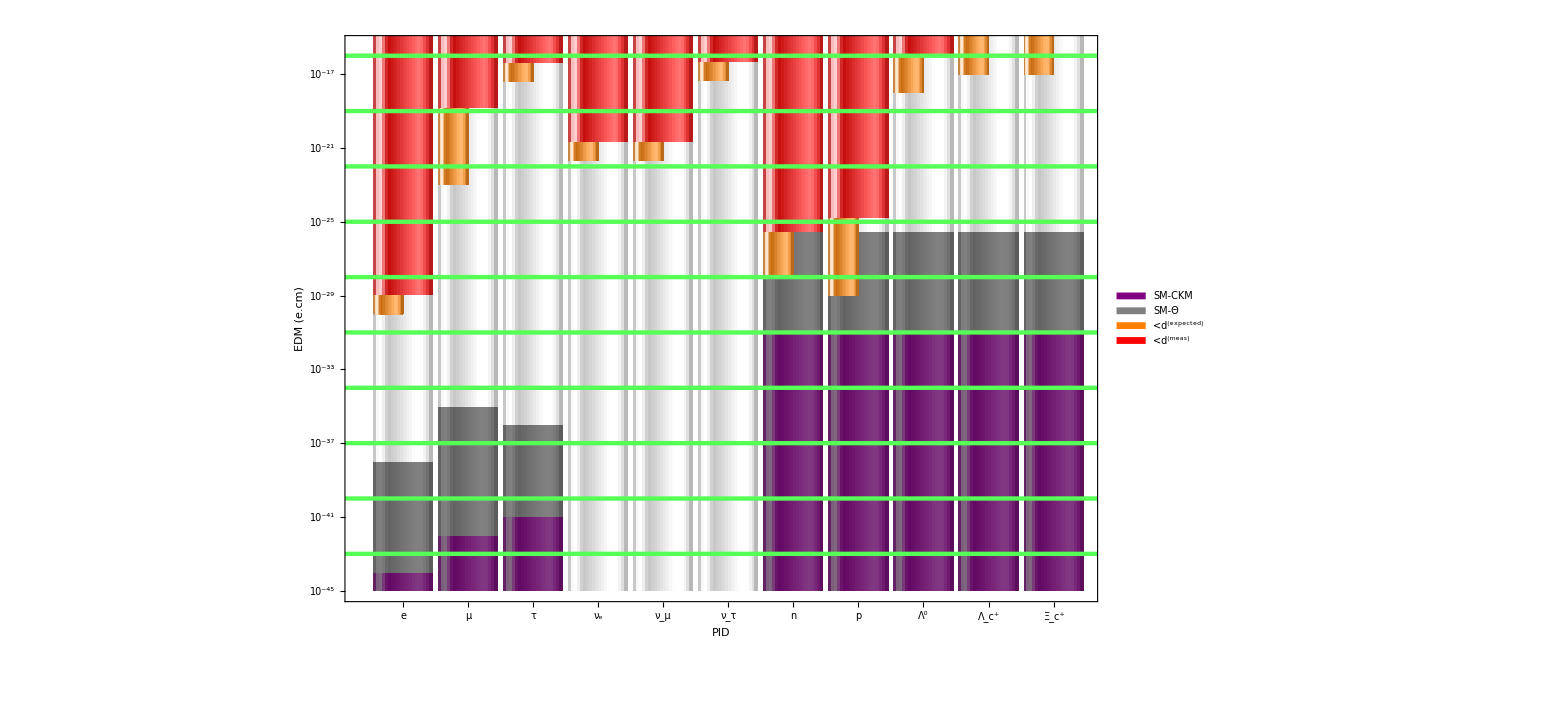

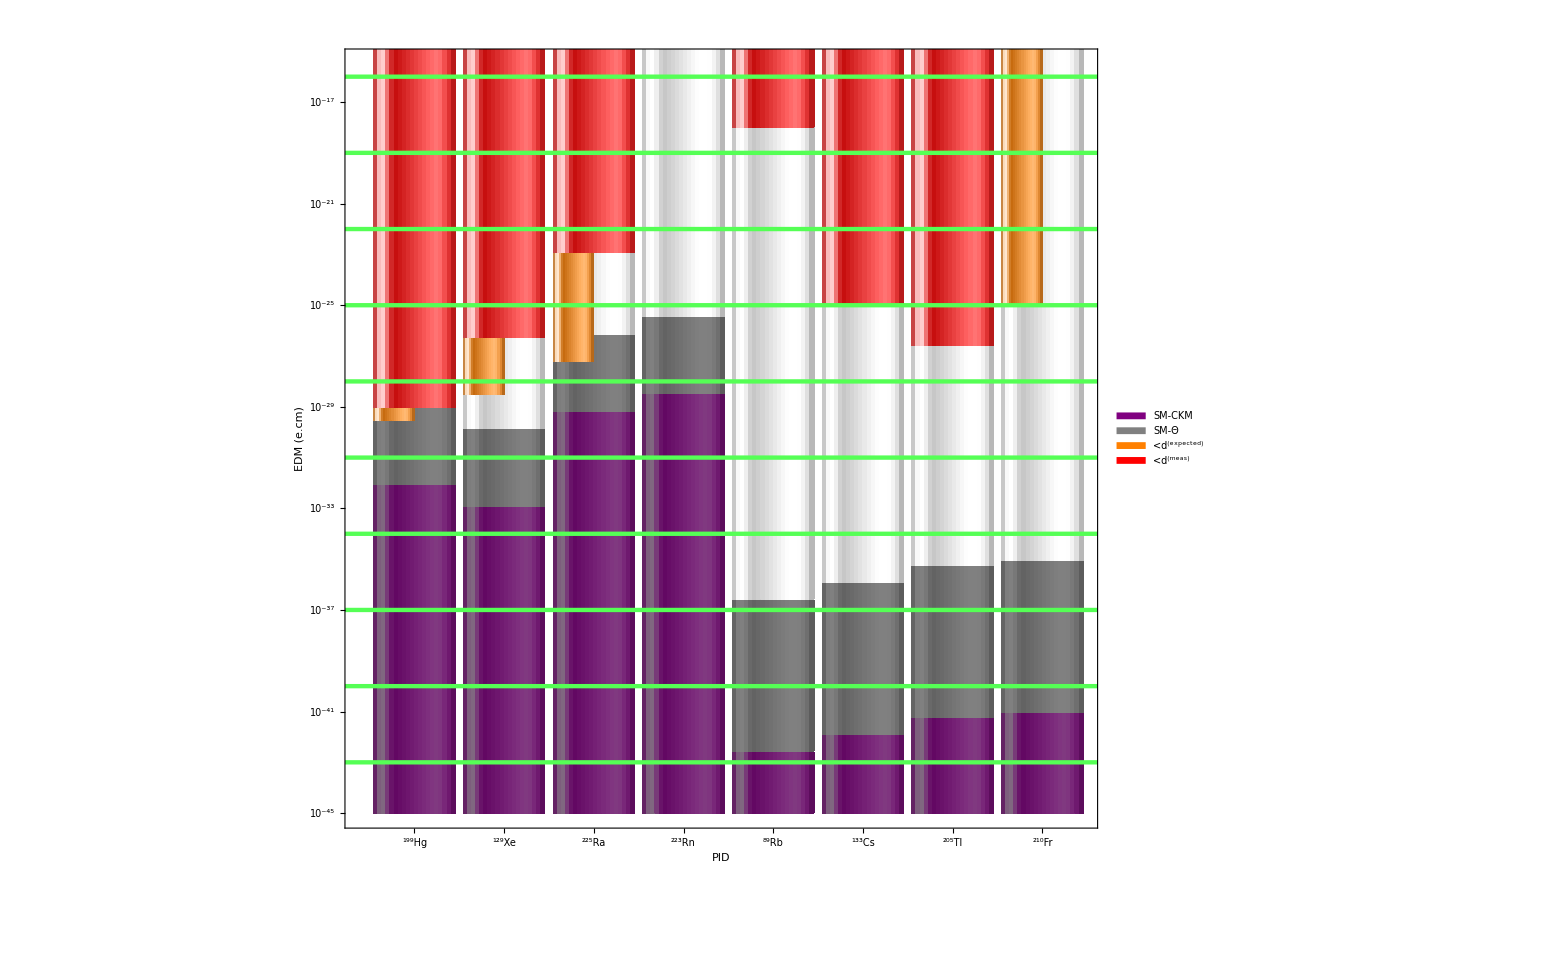

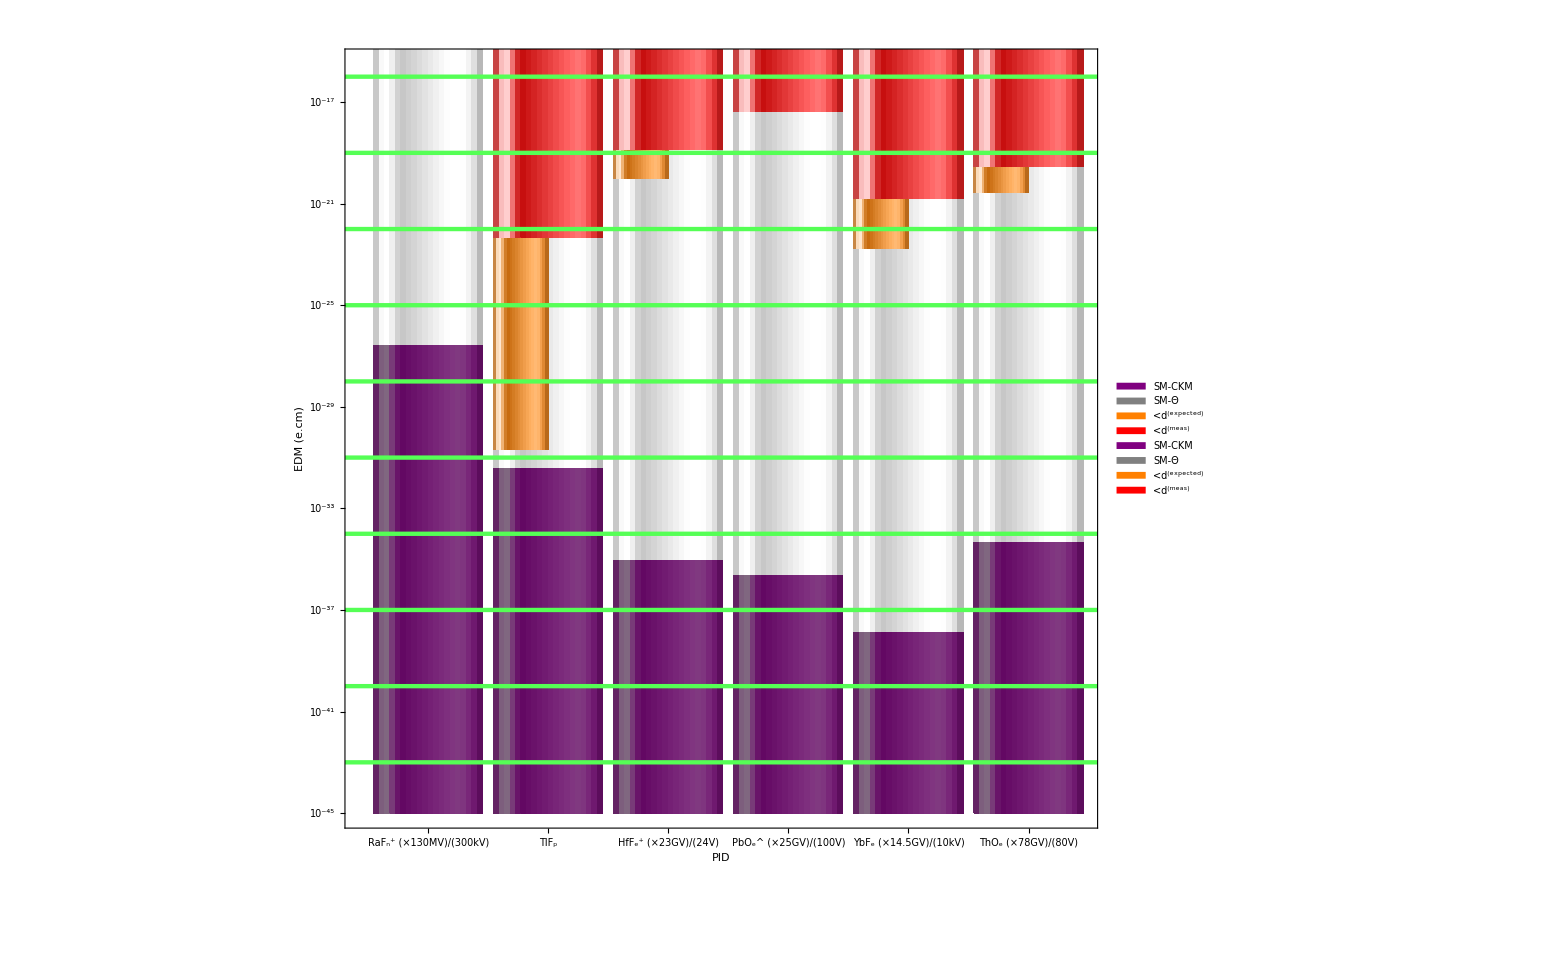

```mathematica
thk=.004;
cht11=RectangleChart[pttab1,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,ImagePadding->120,ChartLegends->Placed[SwatchLegend[{{},{"SM-CKM","SM-Θ","","<d^(expected)","<d^(meas)"}},LegendLayout->{"Row",1}],Top],Frame->True,FrameStyle->Thickness[thk],GridLines->gridln1,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},Epilog->Inset[logo,{4.9,Log@(10^-33)}],TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks1,ChartStyle->{Purple,Gray,Opacity[0,White],Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.2*(numpart/numpart1),ImageSize->1600];
cht12=RectangleChart[pttab12,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,ImagePadding->120,Frame->True,FrameStyle->Thickness[thk],GridLines->gridln1,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},Epilog->Inset[logo,{4.9,Log@(10^-33)}],TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks1,ChartStyle->{Purple,Gray,White,Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.2*(numpart/numpart1),ImageSize->1600];
cht1=Show[{cht12,cht11}]
cht21=RectangleChart[pttab2,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,ImagePadding->120,ChartLegends->Placed[SwatchLegend[{{},{"SM-CKM","SM-Θ","","<d^(expected)","<d^(meas)"}},LegendLayout->{"Row",1}],Top],Frame->True,FrameStyle->Thickness[thk],GridLines->gridln2,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},Epilog->Inset[logo,{6,Log@(10^-31)}],TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks2,ChartStyle->{Purple,Gray,Opacity[0,White],Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.2*(numpart/numpart2),ImageSize->1600];
cht22=RectangleChart[pttab22,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,ImagePadding->120,Frame->True,FrameStyle->Thickness[thk],GridLines->gridln2,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},Epilog->Inset[logo,{6,Log@(10^-31)}],TicksStyle->{Directive[FontSize->32]},
FrameTicks->tks2,ChartStyle->{Purple,Gray,White,Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.2*(numpart/numpart2),ImageSize->1600];
cht2=Show[{cht22,cht21}]
cht31=RectangleChart[pttab3,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,ImagePadding->120,ChartLegends->Placed[SwatchLegend[{{},{"SM-CKM","SM-Θ","","<d^(expected)","<d^(meas)"}},LegendLayout->{"Row",1}],Top],Frame->True,FrameStyle->Thickness[thk],GridLines->gridln3,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},Epilog->Inset[logo,{3.3,Log@(10^-28)}],
FrameTicks->tks3,ChartStyle->{Purple,Gray,Opacity[0,White],Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.2*(numpart/numpart2),ImageSize->1600];cht32=RectangleChart[pttab32,PlotRange->{Automatic,{N[10^(-45)],N[10^(-15.5)]}},(*GridLines->gridln,*)ChartLayout->"Stacked",ScalingFunctions->"Log",BarSpacing->.1,ImagePadding->120,ChartLegends->Placed[SwatchLegend[{{},{"SM-CKM","SM-Θ","","<d^(expected)","<d^(meas)"}},LegendLayout->{"Row",1}],Top],Frame->True,FrameStyle->Thickness[thk],GridLines->gridln3,GridLinesStyle->Directive[Lighter[Green],Thickness[thk/2]],FrameTicksStyle->{Directive[Black,Thickness[thk]],Directive[Black,Thickness[thk]]},FrameLabel->{"PID","EDM (e.cm)"},LabelStyle->{32,Black,Bold},TicksStyle->{Directive[FontSize->32]},Epilog->Inset[logo,{3.3,Log@(10^-28)}],
FrameTicks->tks3,ChartStyle->{Purple,Gray,White,Orange,Red},ChartBaseStyle->EdgeForm[None],ChartElementFunction->"GlassRectangle",AspectRatio->.2*(numpart/numpart2),ImageSize->1600];
cht3=Show[{cht32,cht31}]
```

```mathematica
Export[StringJoin[PicDir,seperator,"EDM_all-t2.png"],cht]
Export[StringJoin[PicDir,seperator,"EDM_fp-t2.png"],cht1]
Export[StringJoin[PicDir,seperator,"EDM_atom-t2.png"],cht2]
Export[StringJoin[PicDir,seperator,"EDM_mol-t2.png"],cht3]
```

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_all-t2.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_fp-t2.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_atom-t2.png

C:\Users\tmpra\Dropbox\nEDM\Pictures\EDM_mol-t2.png

## Data

=== === === === === === === === === =
 *Fundamental Particles*
  ** Charged Leptons ** 
e : {1 E-44[1 b], 1 E-38[1], 8.7 E-29[2]}
Theory comes from light - by - light diagrams
mu : {1 E-42, 1.8 E-35[1], 1.6 E-19[4]}
Here theory values in[1] are simply 1/mass scaled from electrons from[1], [1 b]
tau : {1 E-41, 3.0 E-36, 3.8E-17[5]}
Repeating 1/mass scaling from electrons, muons from[1][1 b]

** Neutrinos ** nu_e: {-, -, 2 E - 21[6]}
Indirect limits : e, e - bar -> Tau, Tau - bar
nu_mu: {-, -, 2 E - 21[6]}
Very similar to nu_e
nu_tau: {-, -, 4.35 E - 17[8, 9]}
Again indirect constraints from ee - bar colliders.Old Constraints in[7, 10] = 5*[8, 9] numbers.Naturalness bounds on MDM & EDMs in[11] for point fermions - leptons and quarks.

** Baryons **
Keeping theta almost the same for all classes of baryons {n, p} & {Lambda, Sigma, Cascade}, unless we' ve a citation elsewhere.
n : {2 E - 32[12, 3], 2.9 E - 26, 2.9 E - 26[13]}
Theory from CKM.
p : {2 E - 32[12, 3], 2.9 E - 26, 1.7 E - 25[21]}
Theory & theta values same as n.[21] uses formalism introduced in[14]

--StrangeBaryons--
Lambda0 - uds : {1 E - 32[16], 4.4 E - 26[17], 1.2 E - 15[16]}
Using d (Lambda)~d (n)/2 in[16].[17 b]~[17], [19] for extra refs.Sigma0 - uds : {3.3 E - 33[18, 19], 4.4 E - 26[17], -}
Using Lambda : Sigma : Cascade = 1 : -1/3 : 4/3 in[18]
Cascade0 - uss : {1.3 E - 32[18, 19], 4.4 E - 26[17], -}
Using Lambda : Sigma : Cascade = 1 : -1/3 : 4/3 in[18]
Lambda + c - udc : {1.3 E - 32[18, 19], 4.4 E - 26[17], -}
[11], [16 b], [17] mention d_c < 4.4 E - 17, but maintaining d_n values for SM - CKM, SM - Theta
Cascade + c - usc : {1.3 E - 32[18, 19], 4.4 E - 26[17], -}
[11], [16 b], [17] mention d_c < 4.4 E - 17, but maintaining d_n values for SM - CKM, SM - Theta

=== === === === === === === === === =
 *Atomic + Molecular*All atomic species which are not extracting eEDM = Ra, Rn, Xe, Pu, are w.r.t 199 Hg in some form for theory.
 
 Hg199 : {8.7 E - 33 < Note >, 1 E - 29[21 b], 6.2 E - 30[21]}
 Projection: 3E-30, https://digital.lib.washington.edu/researchworks/bitstream/handle/1773/40676/Graner_washington_0250E_17909.pdf
< Note > : Includes d_e from[1], d_p & d_n from[12, 3], and plugs them into eq.5.171 using Table - 14 info from[22].(.01 d_e) + (-.56 E - 4 d_p) + (-5.3 E - 4 d_n) = 1.2 E - 35 {If we will assume Hg199 is spherical nuclei and has no Schiff moment contribution.}
(.01 d_e) + (-.56 E - 4 d_p) + (-5.3 E - 4 d_n) + (2.8 E - 7*3.1 E - 13)*1 E - 13 {last 1 E - 13 to convert from e fm to e cm} = 8.7 E - 33, Schiff moment from[23, 23 b], equation to convert to EDM from[22, 23], dominated by Schiff moment, so let' s scale all the remaining species with Schiff moments proportionality (w.r.t EDM) coefficients in[23] abstract.With this 8 E - 33 number, we' d have been~ < 1 E4 from the then experiment limit of 3.1 E - 29 as mentioned in Table 1 of[3 b].[20] is old version of[21]
Ra225 : {6.3 E - 30 < note >, 7.2 E - 27, 1.2 E - 23[26]}
Projection: 6E-28 from https://conferences.lbl.gov/event/137/session/18/contribution/192/material/slides/0.pdf
< note > : EDM factor in front of Schiff moment for Hg199 : 2.8, and Ra225 : 8.5[23] = factor 3. Then Ra225 has octupole deformation~most conservative model enhancement of factor 240 from comparing[24] to[25] (Comes from SIII - SkO' Isovector - a1 comparision, this enhancement could be as large as 1500 from SkM Isoscalar).Also in Table 13 of[22].
Xe129 : {1.2 E - 33 < note >, 1.35 E - 30, 5.4 E - 27[27]}
Projection: 3E-29, from https://indico.cern.ch/event/663474/contributions/3062621/attachments/1682990/2711555/icnfp_2018_edm_FKuchler.pdf, T. Chupp and M. Ramsey-Musolf, PRC 91 (2015) 035502
< note > : Octupole deformation is minimal in Xe[22] Table 12. But from[23] we can get enhancement coming from Schiff moment.Xe129 : 0.38, Hg199 : 2.8 = factor 1/7.4 w.r.t 199 Hg.
Pu239 : {3.4 E - 31 < note >, 4 E - 29, -}
< note > : Schiff factor Pu239 : 11, Hg199 : 2.8 = factor 4 from[23].This also has been suspected of octupole deformation.But no measurement of its octupole deformation or nuclear potential decomposition.Not including in the plot as most likely this estimation is incomplete.No Experiment.
Rn223 : {3.2 E - 29 < note >, 3.7 E - 26, -}
< note > : From[23] Schiff enhancement = factor 1.2 = 3.3 : Rn223/2.8 : Hg199.Then from[28], [22] : Table 12, 13, it has octupole deformation roughly x10 better than Ra225, so x3100.

---eEDM : d_e from[1]-- - 
Tl205 : {573 E - 44 < note >, 573 E - 38, 2.6 E - 27[29]}
< note > 573 d_e[30], [22] : Table 14
Cs133 : {123 E - 44 < note >, 123 E - 38, 9.3 E - 26[31]}
< note > : 123 d_e[32], [22] : Table 14
Rb89 : {25.7 E - 44 < note >, 25.7 E - 38, 1 E - 18[33]}
< note > : 25.7 d_e[32], [22] : Table 14
Fr210 : {903 E - 44 < note >, 903 E - 38, -}
< note > 903 d_e[34], [22] : Table 14, Projection: (903*E-28) from https://indico.cern.ch/event/663474/contributions/3062621/attachments/1682990/2711555/icnfp_2018_edm_FKuchler.pdf
No result yet from Osaka - Tokyo experiment?---molecules-- - Since here the enhancement comes from huge polar - molecular electric field multiples of 10 GV/cm, there are no structural enhancements like for atoms.We will use d_e extracted from each species multiplied by (E_eff/E_lab).This factor will make it look comparable to other experiments without this electric field enhancement, which in polar molecules comes for free.We will also multiply the theory e - EDM with this factor so the theory values will look larger than e - EDM.

---n-molecules---
RaF+ - e*(130/.3 Ra-225) : {2.73E- 27 < note >, 3.12 E - 24, 2.0 E - 19[35, 36 b]}
< note > 300kV/cm=Phys.Rev.Spec.Top. –Acc.and Beams,15,083502 (2012); 130MV/cm=Phys. Rev. A 90 052513 (2014)
---e-molecules---
ThO - e*(80/36 E - 9) : {2.15 E - 35 < note >, 1 E - 29, 2.53 E - 20[35, 35b, 36 b]}
< note > ThO - e : 9.4 E - 29[35], d_e*(Eeff = 80/36 E - 9)[36, 36 b, 35b], (picking 36 V/cm applied over 141 V/cm)
PbO - e*(25/1 E - 7) : {2.5 E - 36 < note >, 2.6 E - 30, 4.3 E - 18[37]}
< note > PbO - e : 1.7 E - 26[37], d_e*(Eeff = 25/.01)[38, 39], 100, 125 V/cm applied.We' ll use 100 V/cm
YbF - e*(14.5/1 E - 5) : {1.45 E - 38 < note >, 1.45 E - 32, 1.54 E - 21[40, 40 b]}
Projection: 1E-30, https://science.energy.gov/~/media/np/nsac/pdf/201610/Holt_NSAC_EDM_20161028.pdf
< note > : YbF - e : 1.06 E - 27[40, 40 b], d_e*(Eeff = 14.5/1 E - 5)[41, 40 b], 10 kV applied.
HfF + -e*(23/24 E - 9) : {1 E - 35 < note >, 9.5 E - 30, 1.25 E - 19[42, 42 b]}
Projection: 1E-20, https://science.energy.gov/~/media/np/nsac/pdf/201610/Holt_NSAC_EDM_20161028.pdf
< note > HfF + -e : 1.3 E - 28[42 b], d_e*(Eeff = 23/24 E - 9)[43, 42 b], 24 V/cm applied
[42 b] has most recent numbers.Old : From[43] we get factor for frequency splitting to EDM = 5.84 E11Hz/(e fm), comparing 4.6 E12Hz/(e fm) for ThO from[22] Table14 given that ThO has an electric field of 84 GV/cm, we can conclude that electric field in HfF + should be~9.9 GV/cm.
---Hybrid Case : TlF-- - 
TlF : {8.3 E - 33 < note >, 1.2 E - 26, 4.8 E - 23[44]}
< note > d_TlF = 573 d_e[30], [22] + d_p/2.4[44]
Projections: Hg-EDM/30 = 2E-31, https://science.energy.gov/~/media/np/nsac/pdf/201610/Holt_NSAC_EDM_20161028.pdf
=== === === === === === === === === = 
Refs : 
[3] Maxim Pospelov, Adam Ritz, Annals Phys.318 (2005) 119 - 169. arXiv : hep - ph/0504231
[3 b] Klaus Jungmann, Annalen Phys.525 (2013) no .8 - 9, 550 - 564. 10.1002/andp .201300071

** Charged Leptons ** 
[1] Diptimoy Ghosh, Ryosuke Sato, Phys.Lett.B777 (2018) 335 - 339. arXiv : 1709.05866
[1 b] F.Hoogeveen, Nucl.Phys.B341 (1990) 322 - 340. 10.1016/0550 - 3213 (90) 90182 - D (only 3 loops = wrong), new= Pospelov, M. & Ritz, A. CKM benchmarks for electron electric dipole moment experiments. Phys. Rev. D 89, 056006 (2014)
[1 c] Werner Bernreuther, Mahiko Suzuki, Rev.Mod.Phys.63 (1991) 313 - 340. Erratum : Rev.Mod.Phys.64 (1992) 633.10 .1103/RevModPhys .63 .313
[2] ACME Collaboration (Jacob Baron et al.), Science 343 (2014) 269 - 272. arXiv : 1310.7534
[4] Muon (g - 2) Collaboration (G.W.Bennett et al.), Phys.Rev.D80 (2009) 052008. arXiv : 0811.1207
[5] Belle Collaboration (K.Inami et al.), Phys.Lett.B551 (2003) 16 - 26. arXiv : hep - ex/0210066

** Neutrinos ** 
[6] F.del Aguila, Marc Sher, Phys.Lett.B252 (1990) 116 - 118. 10.1016/0370 - 2693 (90) 91091 - O
[7] R.Escribano, E.Masso, Phys.Lett.B395 (1997) 369 - 372. arXiv : hep - ph/9609423
[8] Tarek Ibrahim, Pran Nath, Phys.Rev.D81 (2010) no .3, 033007; Erratum : Phys.Rev.D89 (2014) no .11, 119902. arXiv : 1001.0231
[9] R.Escribano, E.Masso, Phys.Lett.B395 (1997) 369 - 372. arXiv : hep - ph/9609423
[10] A.Gutierrez - Rodriguez, M.A.Hernandez - Ruiz, A.Del Rio - De Santiago, Phys.Rev.D69 (2004) 073008. arXiv : hep - ph/0401208
[11] Keiichi Akama, Takashi Hattori, Kazuo Katsuura, Phys.Rev.Lett.88 (2002) 201601. arXiv : hep - ph/0111238


** Baryons ** 
[12] I.B.Khriplovich, A.R.Zhitnitsky, Phys.Lett.109 B (1982) 490 - 492. 10.1016/0370 - 2693 (82) 91121 - 2
[13] nEDM Collaboration (C.A.Baker et al.), Phys.Rev.Lett.97 (2006) 131801. arXiv : hep - ex/0602020
[14] V.F.Dmitriev, R.A.Sen' kov, Phys.Rev.Lett.91 (2003) 212303. arXiv : nucl - th/0306050
[15] L.Pondrom et al., Phys.Rev.D23 (1981) 814 - 816. 10.1103/PhysRevD .23 .814
[16] Antonio Pich, Eduardo de Rafael, Nucl.Phys.B367 (1991) 313 - 333. 10.1016/0550 - 3213 (91) 90019 - T
[16 b] Filippo Sala, JHEP 1403 (2014) 061. DOI : 10.1007/JHEP03 (2014) 061. e - Print : arXiv : 1312.2589
[17] F.J.Botella et al., , Eur.Phys.J.C77 (2017) no .3, 181. arXiv : 1612.06769
[17 b] B.Borasoy, Phys.Rev.D61 (2000) 114017. arXiv : hep - ph/0004011
[18] D.Atwood, A.Soni, Phys.Lett.B291 (1992) 293 - 296. 10.1016/0370 - 2693 (92) 91048 - E
[19] Feng - Kun Guo, Ulf - G.Meissner, JHEP 1212 (2012) 097. arXiv : 1210.5887


** Atoms ** 
[20] M.V.Romalis, W.C.Griffith, E.N.Fortson, Phys.Rev.Lett.86 (2001) 2505 - 2508. arXiv : hep - ex/0012001
[21] B.Graner, Y.Chen, E.G.Lindahl, B.R.Heckel, Phys.Rev.Lett.116 (2016) no .16, 161601. Erratum : Phys.Rev.Lett.119 (2017) no .11, 119901. arXiv : 1601.04339
[21 b] Steven Abel, Oleg Lebedev, JHEP 0601 (2006) 133. arXiv : hep - ph/0508135
[22] Jonathan Engel, Michael J.Ramsey - Musolf, U.van Kolck, Prog.Part.Nucl.Phys.71 (2013) 21 - 74. arXiv : 1303.2371
[23] V.A.Dzuba, V.V.Flambaum, J.S.M.Ginges, M.G.Kozlov, Phys.Rev.A66 (2002) 012111. arxiv : hep - ph/0203202
[23 b] V.V.Flambaum, I.B.Khriplovich, O.P.Sushkov, Phys.Lett.162 B (1985) 213 - 216. 10.1016/0370 - 2693 (85) 90908 - 6
[24] J.H.de Jesus, J.Engel, Phys.Rev.C72 (2005) 045503. arXiv : nucl - th/0507031
[25] J.Dobaczewski, J.Engel, Phys.Rev.Lett.94 (2005) 232502. arXiv : nucl - th/0503057
[26] Michael Bishof et al., Phys.Rev.C94 (2016) no .2, 025501. arXiv : 1606.04931
[27] Rosenberry, M.A., Chupp, T.E., Phys .. Lett.86 (2001) 22 - 25. 10.1103/PhysRevLett .86 .22
[28] V.Spevak, N.Auerbach, V.V.Flambaum, Phys.Rev.C56 (1997) 1357 - 1369. arXiv : nucl - th/9612044
[29] Eugene D.Commins, Stephen B.Ross, David DeMille, B.C.Regan, Phys.Rev.A50 (1994) 2960 - 2977.10 .1103/PhysRevA .50 .2960
[30] Z.W.Liu, Hugh P.Kelly, Phys.Rev.A 45, R4210 (1992).10.1103/PhysRevA .45.R4210
[31] S.A.Murthy, D.Krause, Z.L.Li, L.R.Hunter, Phys.Rev.Lett.63 (1989) 965 - 968. 10.1103/PhysRevLett .63 .965
[32] H.S.Nataraj, B.K.Sahoo, B.P.Das, and D.Mukherjee, Phys.Rev.Lett.101, 033002. 10.1103/PhysRevLett .101 .033002
[33] E.S.Ensberg, Phys.Rev.153 (1967) 36. 10.1103/PhysRev .153 .36
[34] T.M.R.Byrnes, V.A.Dzuba, V.V.Flambaum, and D.W.Murray, Phys.Rev.A 59 (1999) 3082. 10.1103/PhysRevA .59 .3082

** Molecules ** 
[35] ACME Collaboration (Jacob Baron et al.), Science 343 (2014) 269 - 272. arXiv : 1310.7534
[35b] ACME Collaboration, Nature 562, 355–360 (2018).
[36] L.V.Skripnikov, A.V.Titov, J.Chem.Phys.142 (2015) 024301. arXiv : 1410.2485
[36 b] ACME Collaboration (Jacob Baron et al.), New J.Phys.19 (2017) no .7, 073029. arXiv : 1612.09318
[37] S.Eckel, P.Hamilton, E.Kirilov, H.W.Smith, D.DeMille, Phys.Rev.A87 (2013) no .5, 052130. arXiv : 1303.3075
[38] M.G.Kozlov, D.DeMille, Phys.Rev.Lett.89 (2002) 133001. 10.1103/PhysRevLett .89 .133001
[39] A.N.Petrov, A.V.Titov, T.A.Isaev, N.S.Mosyagin, and D.DeMille, Phys.Rev.A 72 (2005) 022505.10 .1103/PhysRevA .72 .022505
[40] J.J.Hudson, D.M.Kara, I.J.Smallman, B.E.Sauer, M.R.Tarbutt, E.A.Hinds, Nature 473 (2011) 493 - 496, 10.1038/nature10104
[40 b] D.M.Kara, I.J.Smallman, J.J.Hudson, B.E.Sauer, M.R.Tarbutt, E.A.Hinds, New J.Phys.14 (2012) 103051. arXiv : 1208.4507
[41] N S Mosyagin et al., 1998 J.Phys.B : At.Mol.Opt.Phys.31 L763.10.1088/0953 - 4075/31/19/002
[42 b] William B.Cairncross et al., Phys.Rev.Lett.119 (2017) no .15, 153001. arXiv : 1704.07928
[42] H.Loh, K.C.Cossel, M.C.Grau, K.-K.Ni, E.R.Meyer, J.L.Bohn, J.Ye, E.A.Cornell, Science Vol.342, Issue 6163 (2013) : 1220 - 1222. 10.1126/science .1243683
[43] A.N.Petrov, N.S.Mosyagin, T.A.Isaev, A.V.Titov, Phys.Rev.A76 (2007) 030501. 10.1103/PhysRevA .76 .030501
[44] D.Cho, K.Sangster, and E.A.Hinds, Phys.Rev.A 44 (1991) 2783. 10.1103/PhysRevA .44 .2783
--

```mathematica
6.3*N[10^(-30)]*130/.3
7.2*N[10^(-27)]*130/.3
```

2.73×10^-27

3.12×10^-24